# Alzheimer’s Detection

### Introduction

-Graphics-

In this project I will be working on MRI data 150 individuals between the age 60-96 to determine if they have Alzheimer’s or not. This data was collected from Open Access Series of Imaging Studies (OASIS)  which makes MRI data available for free for scientific community to perform research in the area. I will be working only on the longitudinal MRI data to create various models using Logistic Regression, Random Forest , Support Vector Machine and Neural networks to check which model functions the best at classifying a patient as demented and not demented. The data that we have was recorded over several visits of same subject and they are all right handed. As per the source this data contains 72 subjects who remain non demented throughout the study, 64 are demented in all visits, 14 are non demented initially and develop Alzheimer over subsequent visits.

DataSource : https://www.kaggle.com/datasets/jboysen/mri-and-alzheimers

### Exploratory Data Analysis

#### Data Introduction

These are the columns available in the longitudinal MRI dataset:

Subject ID - Identification of the subject

MRI ID - MRI exam identification number associated with the subject

Class - This is the class representing if the subject is demented / non demented / other

Visit -  Number representing the visit order

MR Delay - MR Delay time

M/F - Gender of the subject

Hand - Whether the subject is right or left handed

Age - Age of the subject

EDUC - years of education

SES - Socio-economic status

MMSE - mini mental state examination

CDR - Clinical Dementia rating

eTIV - Estimated Total Intercranial Volume

nWBV - Normalize Whole Brain Volume

ASF - Atlas Scaling Factor

#### Data Setup

First I import the data and drop columns that aren’t necessary for EDA or creating classification models.
After this i create 70:30 data split to create a training and testing dataset.

```mathematica
mri =Import["D:\\UCD21-22\\Spring\\Mathematica For Research\\oasis_longitudinal.csv","Dataset","HeaderLines"->1];
(* Drop columns that are not necessary*)
mri = KeyDrop[{"Subject ID", "MRI ID", "Hand"}] @ mri;
(* creating 70% train and 30% test data split*)
rs = RandomSample[Range[Length[mri]]];
train=rs[[1;;Round[Length[mri]*0.7]]];
test=rs[[Round[Length[mri]*.7]+1;;]];
traindata = mri[[train]];
testdata = mri[[test]];
```

#### Correlation

In order to analyse if there is a co-relation among various columns of the dataset, I create a correlation matrix and create a heat-map for the same. Also i consider only numeric columns for this purpose.

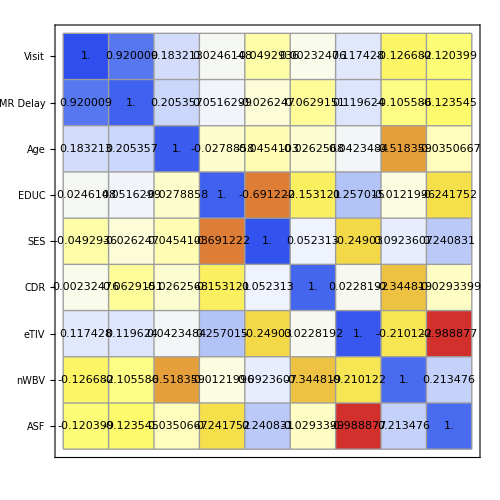

```mathematica
(*using only non numeric columns to check for correlation*)
corr = N[Correlation[Normal[Values@mri[All,{"Visit", "MR Delay", "Age", "EDUC", "SES",  "CDR", "eTIV", "nWBV", "ASF"}]]]];
cols = {"Visit", "MR Delay", "Age", "EDUC", "SES",  "CDR", "eTIV", "nWBV", "ASF"};
ticks={{Table[{i,cols[[i]]},{i,1,Length@cols}],None},{None,Table[{i,cols[[i]]},{i,1,Length@cols}]}};
MatrixPlot[corr,Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[corr],{2}]},Mesh->True,ColorFunction->ColorData[{"Temperature","Reverse"}], ImageSize->500, FrameTicks-> ticks]
```

There is mostly a weak co-relation between a lot of the columns

The few columns that have a strong negative co-relation are ASF and eTIV, SES and EDUC, nWBV and Age.

There is also a positive co-relation between visit and MR Delay showing that each visit the MR Delay value is increasing.

#### Gender Distribution across different Class

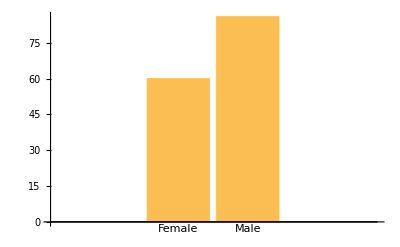

```mathematica
dementia = Select[mri, #Class == "Demented"&];
nondemented = Select[mri, #Class == "Nondemented"&];
converted = Select[mri, #Class == "Converted"&];
BarChart[{Count[Normal@dementia[All, "M/F"] , "F"], Count[Normal@dementia[All, "M/F"] , "M"]}, ChartLabels->{"Female", "Male"}]
```

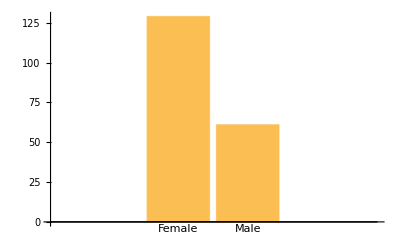

```mathematica
BarChart[{Count[Normal@nondemented[All, "M/F"] , "F"], Count[Normal@nondemented[All, "M/F"] , "M"]}, ChartLabels->{"Female", "Male"}]
```

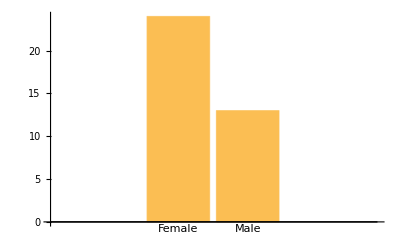

```mathematica
BarChart[{Count[Normal@converted[All, "M/F"] , "F"], Count[Normal@converted[All, "M/F"] , "M"]}, ChartLabels->{"Female", "Male"}]
```

There are more number of males who are demented in this study.

Number of females who are non-demented or converted from non-demented to demented is  high.

#### Relation between SES and EDUC

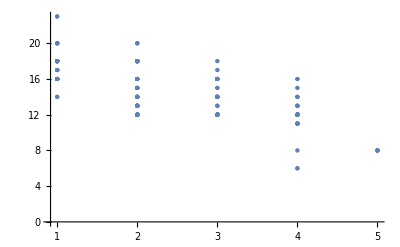

```mathematica
ListPlot[Normal@mri[All, {"SES", "EDUC"}]]
```

This plot further explains the negative co-relation we saw earlier between Socio economic status and number of years spent getting educated. We can see that there is a steady decrease in number of years in education as socio-economic status increases. As no mapping was given what each number of socio economic status means we can deduce that 5 could represent a person of lower economic status and thus spending lesser time on education and person with socio economic status 1 has more resources at hand is able to dedicate more time to education.

#### MMSE Distribution across different Classes

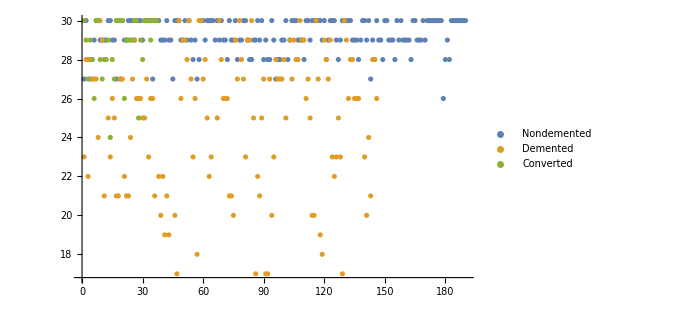

```mathematica
ListPlot[mri[GroupBy["Class"],All, "MMSE"], ImageSize->500]
```

WE can clearly see that Non demented people have an MMSE values ideally between 28-30.

Demented people have MMSE values ranging anywhere between 5 - 30 but is mostly lies between 4-26

For Converted people we can see that initial visits have similar values as non demented people and with later visits the MMSE values drop to the 24-28 region

Just by observing the distribution of MMSE values of demented people(its value distribution is high) we can conclude that this field alone isnt a good enough predictor for determining presence of dementia.

#### Clinical Dementia Rating Distribution

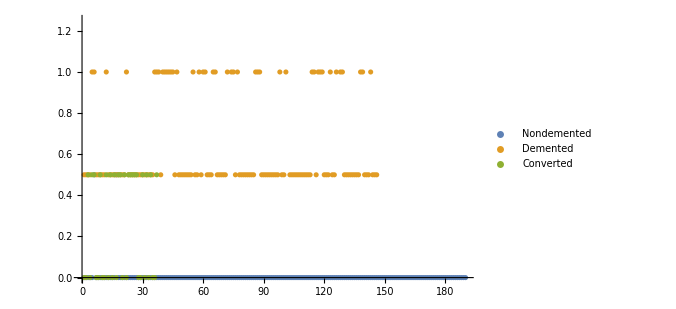

```mathematica
ListPlot[mri[GroupBy["Class"],All, "CDR"], ImageSize->500]
```

Non demented people have a CDR rating of 0

People belonging to the converted class start off with a 0 CDR rating and gradually changes to 0.5

People who are classified as suffering from dementia have a CDR rating of 0.5 or 1 which could also indicate how severely dementia has set in.

#### Age vs Normalized Brain Volume

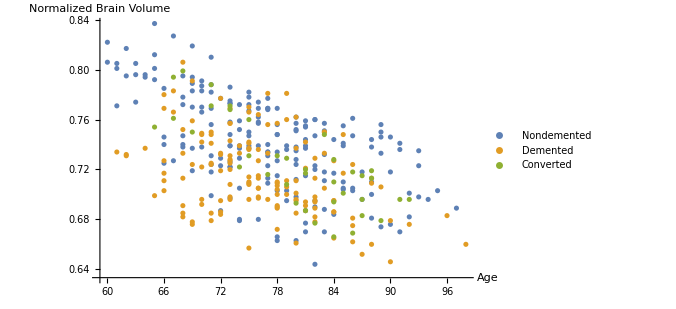

```mathematica
ListPlot[mri[GroupBy["Class"],All, {"Age", "nWBV"}], ImageSize->500, AxesLabel->{"Age", "Normalized Brain Volume"}]
```

This plot is also a representation of the negative co-relation we saw earlier between Age and the normalized brain volume

As age progresses the brain volume is decreasing.

People with dementia show more reduction in brain volume as age progresses compared to non demented people.

### Classification

Based on the EDA performed I will be keeping all the columns to act as predictors for the classification. But before creating the models we need to create associations to both test and train data in the following way:
{“Visit”, “Gender”, “MR Delay”, “Age”, “Hand”,“EDUC”, “SES”,  “CDR”, “eTIV”, “nWBV”, “ASF”} -> {Class} 
As per my dataset structure the Class column appears first so i use the Rest and First functions to create the association.

```mathematica
finalTrain = Flatten[Normal @ traindata[All, {Rest@#-> First@#}&],1];
finalTest = Flatten[Normal @ testdata[All, {Rest@#-> First@#}&],1];
```

#### Logistic Regression

Logistic Regression is a method that models the log probabilities of each class for the set of predictors passed.

```mathematica
modLog = Classify[finalTrain,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
CM = ClassifierMeasurements[modLog, finalTest];
CM["Accuracy"]
```

0.883929

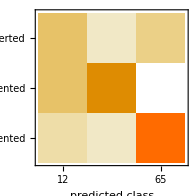

```mathematica
CM["ConfusionMatrixPlot"]
```

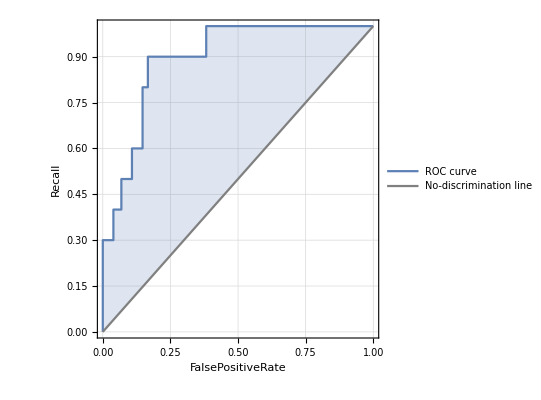
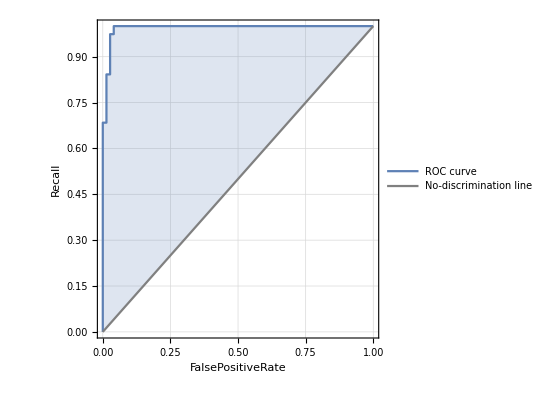
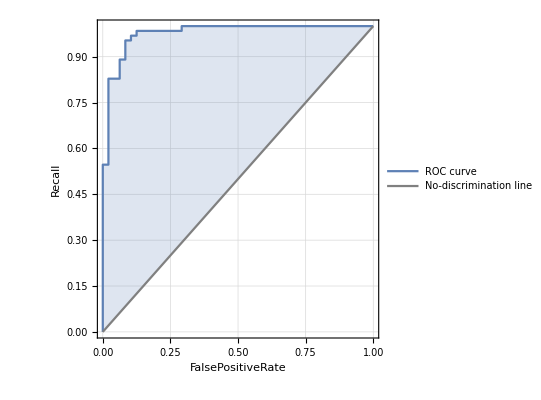
<|Converted→-Graphics-,Demented→-Graphics-,Nondemented→-Graphics-|>

```mathematica
CM["ROCCurve"]
```

#### Support Vector Machine

Support vector Machine is a supervised learning algorithm which works by finding a hyperplane in the n dimension(where n represents the number of predictors) which helps classify the data points.

```mathematica
modSVM=Classify[finalTrain,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
CMSVM = ClassifierMeasurements[modSVM, finalTest];
CMSVM["Accuracy"]
```

0.892857

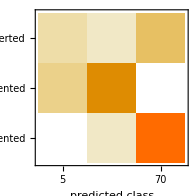

```mathematica
CMSVM["ConfusionMatrixPlot"]
```

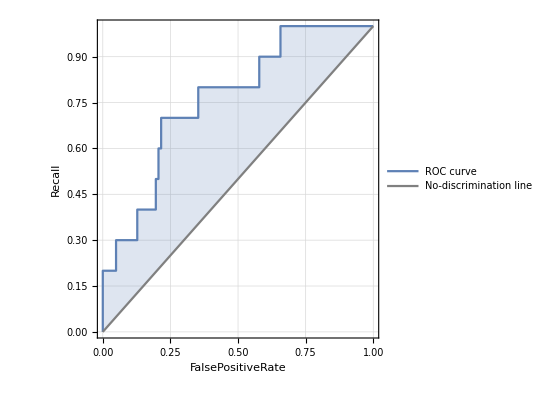
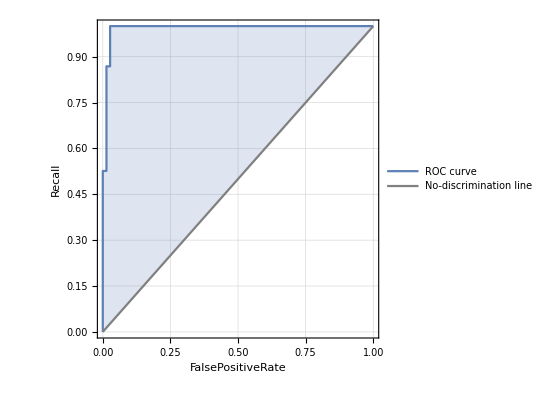
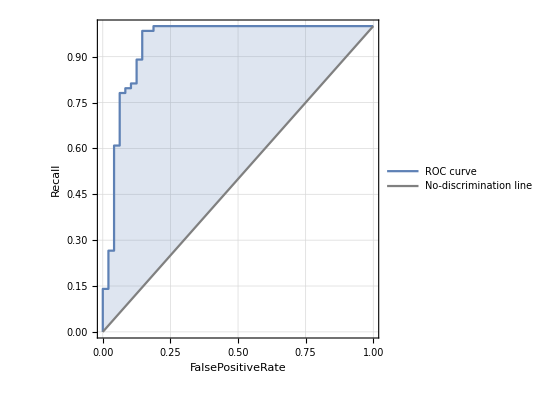
<|Converted→-Graphics-,Demented→-Graphics-,Nondemented→-Graphics-|>

```mathematica
CMSVM["ROCCurve"]
```

#### Random Forest

Random Forest is also a supervised learning algorithm which creates decision trees for classification purpose using bagging technique which increases accuracy in each iteration.

```mathematica
modRF=Classify[finalTrain,Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
CMRF = ClassifierMeasurements[modRF, finalTest];
CMRF["Accuracy"]
```

0.901786

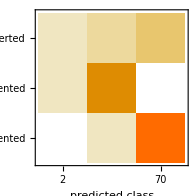

```mathematica
CMRF["ConfusionMatrixPlot"]
```

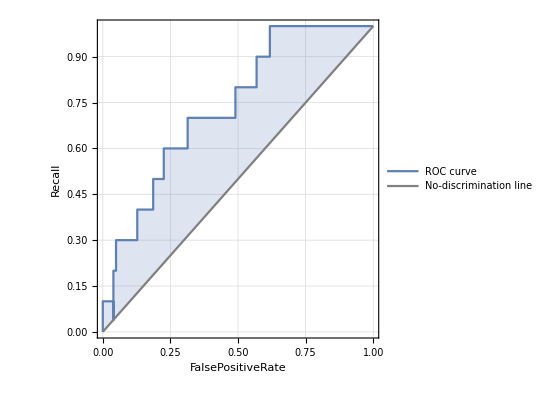
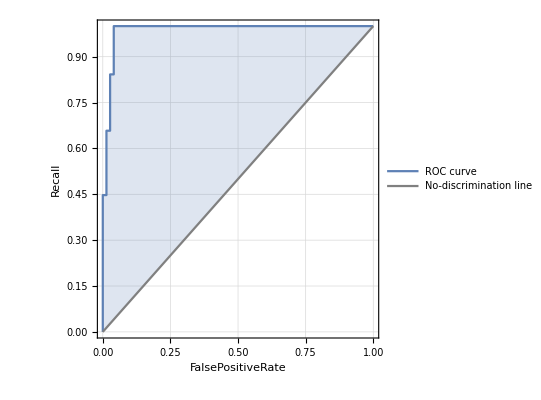
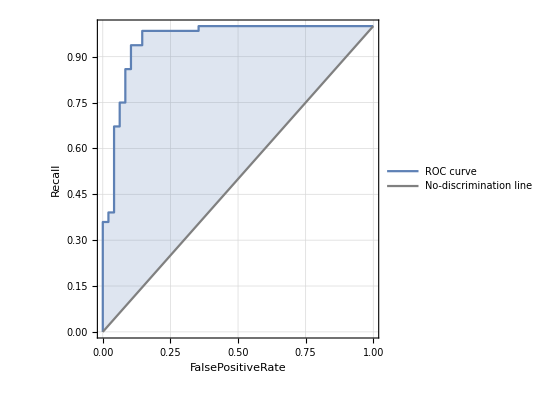
<|Converted→-Graphics-,Demented→-Graphics-,Nondemented→-Graphics-|>

```mathematica
CMRF["ROCCurve"]
```

#### Neural Network

Neural networks is a  deep learning algorithm that recognizes relationship between data to help classify . It consists of multiply layers that are interconnected and behave like the neurons of human brain.

```mathematica
modNN = Classify[finalTrain,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
CMNN = ClassifierMeasurements[modNN, finalTest];
CMNN["Accuracy"]
```

0.901786

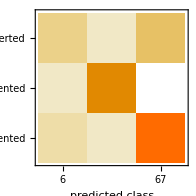

```mathematica
CMNN["ConfusionMatrixPlot"]
```

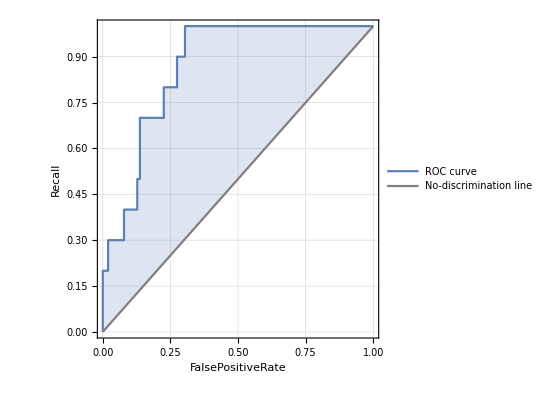
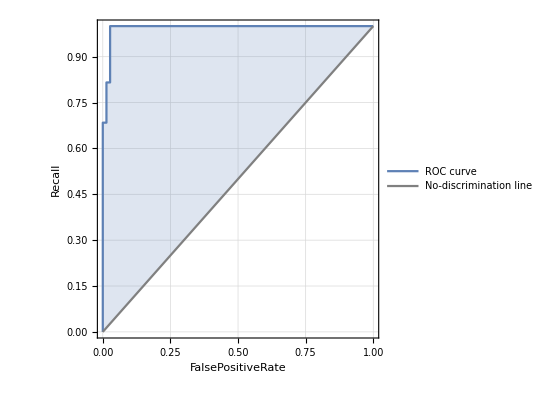
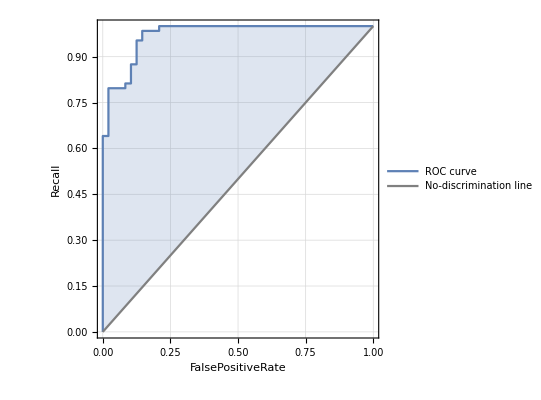
<|Converted→-Graphics-,Demented→-Graphics-,Nondemented→-Graphics-|>

```mathematica
CMNN["ROCCurve"]
```

### Conclusion

Based on the accuracy Random Forest is the model which is classifying data best. All the algorithms are having issues classifying people who fall in the converted category correctly. This could be due such a big intersection in data between demented and non-demented. We would definitely need more data points and features to be able to classify the converted category correctly. The ROC curves also represent similar statistics as the confusion matrix. For all algorithms the ROC curve is quite far from the 45 degree line indicating good classification but its not the case for converted class which shows poor classification for all algorithms.